## Discrete Fourier Transform (Test)

```mathematica
ClearAll["Global*`"]
```

Implement function for transforming degrees to radians

```mathematica
rad[deg_]:=deg*π/180;
deg[rad_]:=rad*180/π;
```

### Create mapper function

The mapper function takes a pure function f that depends on one argument and applies it to an entire list of sampled-data points (N-data points)

```mathematica
mapper[function_,data_]:=Map[function,data];
export[path_,object_]:=Export[StringTemplate["````.pdf"][NotebookDirectory[],path],object,ImageSize->Large];
```

### Generate a sampled data with fixed size

```mathematica
xdataRaw[N_]:=Table[deg,{deg,60/N,60,60/N}];
xdata[N_]:=mapper[rad,xdataRaw[N]];
```

## Generate the function data points from the function method itself

### the function “f2” has an additional phase shift as compared to “f1”

### test function “f”

```mathematica
(*declare a constant phase to be used within calculations*)
phase=45;
f1[x_]:=2Sin[x]+Sin[3x];
f2[x_]:=2Sin[x+rad[phase]]+Sin[3x];
mydata=xdata[30];
mydata
```

{π/90,π/45,π/30,(2 π)/45,π/18,π/15,(7 π)/90,(4 π)/45,π/10,π/9,(11 π)/90,(2 π)/15,(13 π)/90,(7 π)/45,π/6,(8 π)/45,(17 π)/90,π/5,(19 π)/90,(2 π)/9,(7 π)/30,(11 π)/45,(23 π)/90,(4 π)/15,(5 π)/18,(13 π)/45,(3 π)/10,(14 π)/45,(29 π)/90,π/3}

## Create plot data from the given function values

```mathematica
f1ydata[data_]:=N[mapper[f1,data]];
f2ydata[data_]:=N[mapper[f2,data]];
```

## Create graphical representation with the function values

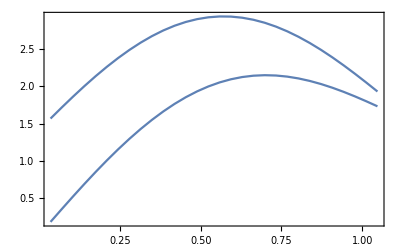

```mathematica
plotter[xdata_,ydata_]:=ListPlot[Table[{xdata[[i]],ydata[[i]]},{i,1,Length[xdata]}],Joined->True,Frame->True,Axes->False];
Show[plotter[mydata,f1ydata[mydata]],plotter[mydata,f2ydata[mydata]],PlotRange->Full]
```

```mathematica
findex[function_,data_,id_]:=function[data][[id]];
fk[k_,data_]:=findex[f1ydata,data,k+1];
```

## Create exponential function for Discrete Fourier Transform

```mathematica
exp[n_,k_,N_]:=Exp[-2π*ⅈ*n*k*1/N];
```

## Create a Fourier component F_n

```mathematica
Fn[n_,data_]:=Sum[Table[fk[k,data]*exp[n,k,Length[data]],{k,0,Length[data]-1}][[i]],{i,1,Length[Table[fk[k,data]*exp[n,k,Length[data]],{k,0,Length[data]-1}]]}];
```

```mathematica
Do[Print[Fn[n,mydata]],{n,0,5}]
```

48.5921

-7.96282+6.97277 ⅈ

-2.24273+3.49303 ⅈ

-1.40106+2.28717 ⅈ

-1.119+1.66953 ⅈ

-0.990767+1.2876 ⅈ

## Compare Re with Im

```mathematica
Do[Print[Fn[n,mydata]," ",Re[Fn[n,mydata]]," ",Im[Fn[n,mydata]]],{n,0,5}]
```

48.5921 48.5921 0

-7.96282+6.97277 ⅈ -7.96282 6.97277

-2.24273+3.49303 ⅈ -2.24273 3.49303

-1.40106+2.28717 ⅈ -1.40106 2.28717

-1.119+1.66953 ⅈ -1.119 1.66953

-0.990767+1.2876 ⅈ -0.990767 1.2876